# Solving the Schrödinger Equation for Finite Potentials: From Atoms to Molecules to Solids.

Terry Cevallos, Milagros Delgado, Daheny López, Quray Potosí, and Ángel Salazar
School of Physical Sciences and Nanotechnology, Yachay Tech University, Urcuquí-Ecuador

## Single Finite potential Well: Model of a Single Atom

### Define the potential

Let’s define the potential and visualize (for inserting {, use EscpwEsc, and to add spaces, use Ctrlenter):

```mathematica
v[x_]:= Piecewise[{{v0, x<-a/2}, {0, -a/2 <= x <=a/2}, {v0, x> a/2}}]
```

Setting values of the variables : width (a) and height (v0pot) of the potential :

```mathematica
la=2 (*Bohr*);
vpot = 6.5 (*Subscript[E, h] (Hartree)*);
```

Visualizing the potential:

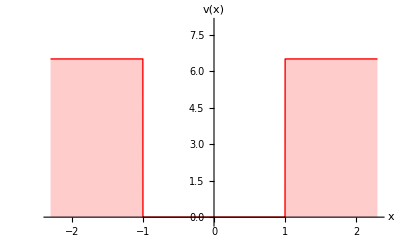

```mathematica
Plot[ v[x]/.{v0-> vpot,a->la}, {x,-la-0.3,la+0.3} ,
AxesLabel->{"x","v(x)"},
PlotStyle->{Red, Thick},
PlotRange->{Automatic,{-0.2,vpot+1.5}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis
]
```

### Solving the Schrodinger equation in a.u

In atomic units: ℏ → 1, m→ 1, e → 1. Then, lengths are given in Bohr (1 Bohr = 0.53 Å) and energies in Hartree (E_h =2721 eV).

Let's define α =√(2 (v0 - ℰ)), β =√(2 ℰ), where ℰ is the energy (ℰ is EscscEEsc and ϕ is EscfEsc):

```mathematica
Do[Subscript[c,i]= .,{i,4}];
Do[Subscript[ϕ, i]=.,{i,3}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
Subscript[ϕ, 2][x_]:=Subscript[c, 2] Cos[β x]+ Subscript[c, 3] Sin [β x];
Subscript[ϕ, 3][x_]:=Subscript[c, 4] Exp[-α x];
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ϕ_1 not found.

Unset::norep: Assignment on Subscript for ϕ_2 not found.

Unset::norep: Assignment on Subscript for ϕ_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Let’s define the wavefunction ϕ (x):

(φ is EscjEsc)

```mathematica
φ[x_]:= Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2 <= x <=a/2}, {Subscript[ϕ, 3][x], x> a/2}}]
```

Defining the BCs :

```mathematica
eq[1]=(Subscript[ϕ, 1][x]-Subscript[ϕ, 2][x]/. x->-a/2 )==0;
eq[2]=(Subscript[ϕ, 1]'[x]-Subscript[ϕ, 2]'[x]/. x->-a/2 )==0;
eq[3]=(Subscript[ϕ, 2][x]-Subscript[ϕ, 3][x]/. x->a/2 )==0;
eq[4]=(Subscript[ϕ, 2]'[x]-Subscript[ϕ, 3]'[x]/. x->a/2 )==0;
```

Solving the BC equations:

The way to solve this is by making the determinant of the matrix of the BCs equation == 0.

```mathematica
mat = CoefficientArrays[Table[eq[i],{i,4}], Table[Subscript[c, i],{i,4}]][[2]]//Normal
```

{{ⅇ^(-(a α)/2),-Cos[(a β)/2],Sin[(a β)/2],0},{ⅇ^(-(a α)/2) α,-β Sin[(a β)/2],-β Cos[(a β)/2],0},{0,Cos[(a β)/2],Sin[(a β)/2],-ⅇ^(-(a α)/2)},{0,-β Sin[(a β)/2],β Cos[(a β)/2],ⅇ^(-(a α)/2) α}}

```mathematica
mat//MatrixForm
```

(ⅇ^(-(a α)/2) | -Cos[(a β)/2] | Sin[(a β)/2] | 0
ⅇ^(-(a α)/2) α | -β Sin[(a β)/2] | -β Cos[(a β)/2] | 0
0 | Cos[(a β)/2] | Sin[(a β)/2] | -ⅇ^(-(a α)/2)
0 | -β Sin[(a β)/2] | β Cos[(a β)/2] | ⅇ^(-(a α)/2) α)

```mathematica
mat2=mat/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la}//FullSimplify
```

{{ⅇ^(-1.41421 √(6.5-ℰ)),-Cos[√2 √ℰ],Sin[√2 √ℰ],0},{1.41421 ⅇ^(-1.41421 √(6.5-ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[√2 √ℰ],-√2 √ℰ Cos[√2 √ℰ],0},{0,Cos[√2 √ℰ],Sin[√2 √ℰ],-ⅇ^(-1.41421 √(6.5-ℰ))},{0,-√2 √ℰ Sin[√2 √ℰ],√2 √ℰ Cos[√2 √ℰ],1.41421 ⅇ^(-1.41421 √(6.5-ℰ)) √(6.5-ℰ)}}

Plotting the determinant:

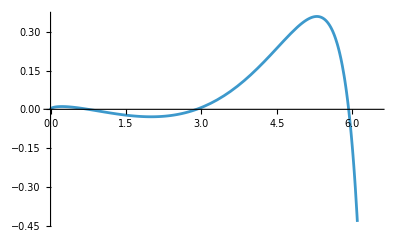

```mathematica
Plot[Det[mat2],{ℰ,0,vpot}]
```

The number of roots of the determinant indicates the number of energy levels of the system, and the value of these roots indicates the amount of energy at each energy level .

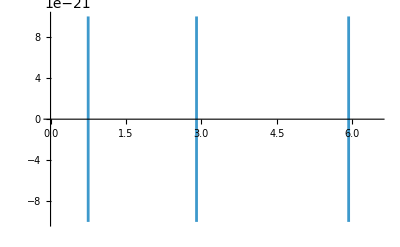

```mathematica
fig=Plot[Det[mat2],{ℰ,0,vpot},PlotRange->{-10^-20,10^-20}] (*Not a special reason for this range; it only has to be very small.*)
```

We observe 3 roots, meaning that this system has 3 energy levels.

Finding the eigenvalues of the energy:

To know the real values with FindRoot function, first we have to make a guess of those roots, otherwise the computing time will be more extended.

```mathematica
approxroots= 
fig[[1,1,1,1,3,1]][[2;;-1]]//Map[#[[1,1,1]]&,#]&//Sort
```

{0.748476,2.9027,5.92702}

```mathematica
rval= approxroots//Map[FindRoot[Det[mat2],{ℰ,#}]&,#]&//
Map[ℰ/.#&,#]&
```

{0.7495,2.9032,5.92714}

### Calculating the energies by levels:

#### Level 1

```mathematica
nval=1;
Do[Subscript[c,i]=.,{i,4}];
Evaluate[Table[Subscript[c, i],{i,4}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{0.705376,0.0699299,0,0.705376}

These are the constants c_1, c_2, c_3, c_4.

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[φ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.00633217

Visualizing the wavefunctions and PDFs:

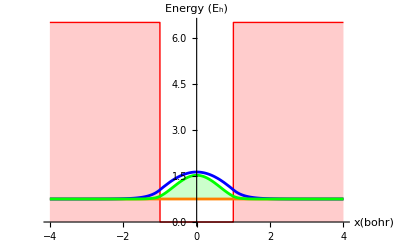

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)φ[x],
ℰ+(1/(√int)φ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}//
Evaluate,{x,-la-2,la+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green}, (*Orange is for the energy levels, blue for the wavefunction, and green for the probability density.*)
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

Barrier penetration: the probability of the electron being outside the well is not zero. This is because of Heisenberg uncertainty principle (Δx Δp ≥ ℏ/2).
Is it possible to measure the wavefunction? No, only the wavefunction squared (PDE).

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at x > a/2?

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,la/2,∞}]
```

0.0131291

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]* x 1/(√int)φ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.9999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 1.04083×10^-17 and 3.83571×10^-14 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]* x^2 1/(√int)φ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.228641

Then, Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

0.478165

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]* (-ⅈ D[  1/(√int)φ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-3.84928×10^-6}. NIntegrate obtained 0.+8.66142×10^-17 ⅈ and 1.19079×10^-16 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]* (-D[  1/(√int)φ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

1.15764

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

1.07594

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

0.514476

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)φ[x]* (-1/2 D[  1/(√int)φ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.578822

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)φ[x]* v[x] 1/(√int) φ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.170678

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

0.7495

```mathematica
ℰ/.ℰ->rval[[nval]]
```

0.7495

#### Level 2

```mathematica
nval=2;
Do[Subscript[c,i]=.,{i,4}];
Evaluate[Table[Subscript[c, i],{i,4}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.705261,0,0.0722025,0.705261}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[φ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.00715691

Visualizing the wavefunctions and PDFs:

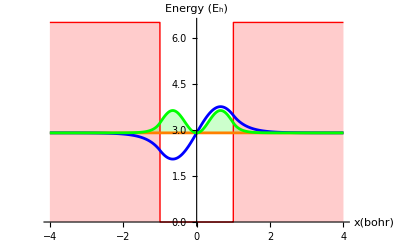

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)φ[x],
ℰ+(1/(√int)φ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}//
Evaluate,{x,-la-2,la+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

Barrier penetration: the probability of the electron being outside the well is not zero. This is because of Heisenberg uncertainty principle (Δx Δp ≥ ℏ/2).
Is it possible to measure the wavefunction? No, only the wavefunction squared (PDE).

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at x > a/2?

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,la/2,∞}]
```

0.0606513

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]* x 1/(√int)φ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 3.98986×10^-16 and 1.46282×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]* x^2 1/(√int)φ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.548414

Then, Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

0.74055

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]* (-ⅈ D[  1/(√int)φ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.0000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 0.+7.89299×10^-16 ⅈ and 1.58366×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]* (-D[  1/(√int)φ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

4.22948

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.05657

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

1.52299

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)φ[x]* (-1/2 D[  1/(√int)φ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.11474

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)φ[x]* v[x] 1/(√int) φ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.788467

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

2.9032

```mathematica
ℰ/.ℰ->rval[[nval]]
```

2.9032

#### Level 3

```mathematica
nval=3;
Do[Subscript[c,i]=.,{i,4}];
Evaluate[Table[Subscript[c, i],{i,4}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.685361,-0.24609,0,0.685361}

These are the constants c_1, c_2, c_3, c_4.

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[φ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.117138

Visualizing the wavefunctions and PDFs:

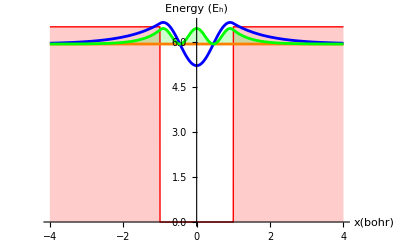

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)φ[x],
ℰ+(1/(√int)φ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}//
Evaluate,{x,-la-2,la+2},
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

Barrier penetration: the probability of the electron being outside the well is not zero. This is because of Heisenberg uncertainty principle (Δx Δp ≥ ℏ/2).
Is it possible to measure the wavefunction? No, only the wavefunction squared (PDE).

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at x > a/2?

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,la/2,∞}]
```

0.220218

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)φ[x]* x 1/(√int)φ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.804656}. NIntegrate obtained -6.84348×10^-16 and 9.51797×10^-17 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)φ[x]* x^2 1/(√int)φ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

1.27519

Then, Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

1.12924

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)φ[x]* (-ⅈ D[  1/(√int)φ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.99999998206481784018499997731624644344006203056096637737937271595}. NIntegrate obtained 0.-6.245×10^-16 ⅈ and 9.10146×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)φ[x]* (-D[  1/(√int)φ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

6.12863

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.47561

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

2.79556

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)φ[x]* (-1/2 D[  1/(√int)φ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

3.06431

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)φ[x]* v[x] 1/(√int) φ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.86283

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

5.92714

```mathematica
ℰ/.ℰ->rval[[nval]]
```

5.92714

### Summary of the plots

Level 1 corresponds to the s orbital (0 nodes).
Level 2  corresponds to the p orbital (1 node).
Level 3  corresponds to the d orbital (2 nodes).

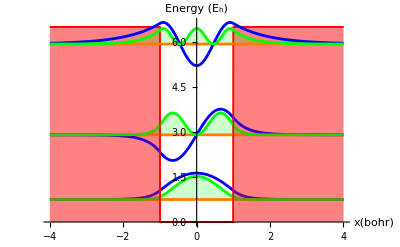

```mathematica
Show@@Table[figure[i],{i,3}]
```

Barrier penetration is higher as you go higher in energy.

1. What is the total energy of the system if it has 3 electrons?

In level 1, it contains 2 electrons, while in level 2, only 1 electron:

```mathematica
Subscript[ℰ, tot][atom]=2 rval[[1]]+rval[[2]]
```

4.40221

2.  What is the total kinetic energy of the 3 electrons?

```mathematica
Subscript[k, tot]=2 ⟨Subscript[k, 1]⟩+⟨Subscript[k, 2]⟩
```

3.27238

3. What is the total potential energy of 3 electrons?

```mathematica
Subscript[u, tot]= 2 ⟨Subscript[u, 1]⟩ +⟨Subscript[u, 2]⟩
```

1.12982

Notice that ℰ_tot = k_tot + u_tot:

```mathematica
Subscript[k, tot]+Subscript[u, tot]
```

4.40221

## Two Finite Potential Wells: Model of a Diatomic Molecule

### Define the potential

Let’s define the potential and visualize (for inserting {, use EscpwEsc, and to add spaces, use Ctrlenter):

```mathematica
v[x_]:= Piecewise[{{v0, x<-b/2-a}, {0, -b/2-a <= x <=-b/2}, {v0, -b/2<x<b/2}, {0, b/2<=x<=a+b/2}, {v0, x>a+b/2}}]
```

Setting values of the variables : width (a) and height (v0pot) of the potential :

```mathematica
la=2 (*Bohr*);
lb=1 (*Bohr*);
vpot = 6.5 (*Subscript[E, h] (Hartree)*);
```

Visualizing the potential:

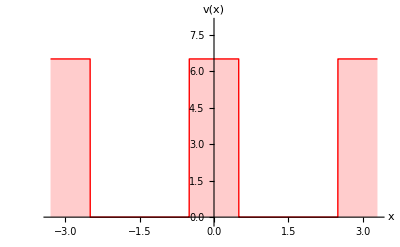

```mathematica
Plot[ v[x]/.{v0-> vpot,a->la,b->lb}, {x,-la-lb-0.3,la+lb+0.3} ,
AxesLabel->{"x","v(x)"},
PlotStyle->{Red, Thick},
PlotRange->{Automatic,{-0.2,vpot+1.5}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis
]
```

### Solving the Schrodinger equation in a.u

In atomic units: ℏ → 1, m→ 1, e → 1. Then, lengths are given in Bohr (1 Bohr = 0.53 Å) and energies in Hartree (E_h =2721 eV).

Let's define α =√(2 (v0 - ℰ)), β =√(2 ℰ), where ℰ is the energy (ℰ is EscscEEsc and ϕ is EscfEsc):

We have 5 regions (5 associated wavefunctions), and 4 BCs.
In regions where V = 0, the solution take the form of cos(x) + sin(x). On the other hand, in regions where V = v0, the solutions take the form of exponentials.

```mathematica
Do[Subscript[c,i]= .,{i,8}];
Do[Subscript[ϕ, i]=.,{i,5}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
Subscript[ϕ, 2][x_]:=Subscript[c, 2] Cos[β x]+ Subscript[c, 3] Sin [β x];
Subscript[ϕ, 3][x_]:=Subscript[c, 4] Exp[-α x]+Subscript[c, 5] Exp[α x];
Subscript[ϕ, 4][x_]:=Subscript[c, 6] Cos[β x]+Subscript[c, 7] Sin[β x];
Subscript[ϕ, 5][x_]:=Subscript[c, 8] Exp[-α x];
```

Unset::norep: Assignment on Subscript for c_5 not found.

Unset::norep: Assignment on Subscript for c_6 not found.

Unset::norep: Assignment on Subscript for c_7 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ϕ_1 not found.

Unset::norep: Assignment on Subscript for ϕ_2 not found.

Unset::norep: Assignment on Subscript for ϕ_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Let’s define the wavefunction ϕ (x):

(ϕ is Esc phi Esc)

```mathematica
ϕ[x_]:=Piecewise[{{Subscript[ϕ, 1][x], x<-b/2-a}, {Subscript[ϕ, 2][x], -b/2-a <= x <=-b/2}, {Subscript[ϕ, 3][x], -b/2<x<b/2}, {Subscript[ϕ, 4][x], b/2<=x<=a+b/2}, {Subscript[ϕ, 5][x], x>a+b/2}}]
```

Defining the BCs:

```mathematica
eq[1]=(Subscript[ϕ, 1][x]-Subscript[ϕ, 2][x]/. x->-b/2-a )==0;
eq[2]=(Subscript[ϕ, 1]'[x]-Subscript[ϕ, 2]'[x]/. x->-b/2-a )==0;
eq[3]=(Subscript[ϕ, 2][x]-Subscript[ϕ, 3][x]/. x->-b/2 )==0;
eq[4]=(Subscript[ϕ, 2]'[x]-Subscript[ϕ, 3]'[x]/. x->-b/2 )==0;
eq[5]=(Subscript[ϕ, 3][x]-Subscript[ϕ, 4][x]/. x->b/2 )==0;
eq[6]=(Subscript[ϕ, 3]'[x]-Subscript[ϕ, 4]'[x]/. x->b/2 )==0;
eq[7]=(Subscript[ϕ, 4][x]-Subscript[ϕ, 5][x]/. x->a+b/2 )==0;
eq[8]=(Subscript[ϕ, 4]'[x]-Subscript[ϕ, 5]'[x]/. x->a+b/2 )==0;
```

Solving the BC equations:

The way to solve this is by making the determinant of the matrix of the BCs equations == 0.

```mathematica
mat = CoefficientArrays[Table[eq[i],{i,8}], Table[Subscript[c, i],{i,8}]][[2]]//Normal
```

{{ⅇ^((-a-b/2) α),-Cos[(-a-b/2) β],-Sin[(-a-b/2) β],0,0,0,0,0},{ⅇ^((-a-b/2) α) α,β Sin[(-a-b/2) β],-β Cos[(-a-b/2) β],0,0,0,0,0},{0,Cos[(b β)/2],-Sin[(b β)/2],-ⅇ^((b α)/2),-ⅇ^(-(b α)/2),0,0,0},{0,β Sin[(b β)/2],β Cos[(b β)/2],ⅇ^((b α)/2) α,-ⅇ^(-(b α)/2) α,0,0,0},{0,0,0,ⅇ^(-(b α)/2),ⅇ^((b α)/2),-Cos[(b β)/2],-Sin[(b β)/2],0},{0,0,0,-ⅇ^(-(b α)/2) α,ⅇ^((b α)/2) α,β Sin[(b β)/2],-β Cos[(b β)/2],0},{0,0,0,0,0,Cos[(a+b/2) β],Sin[(a+b/2) β],-ⅇ^(-((a+b/2) α))},{0,0,0,0,0,-β Sin[(a+b/2) β],β Cos[(a+b/2) β],ⅇ^(-((a+b/2) α)) α}}

```mathematica
mat//MatrixForm
```

(ⅇ^((-a-b/2) α) | -Cos[(-a-b/2) β] | -Sin[(-a-b/2) β] | 0 | 0 | 0 | 0 | 0
ⅇ^((-a-b/2) α) α | β Sin[(-a-b/2) β] | -β Cos[(-a-b/2) β] | 0 | 0 | 0 | 0 | 0
0 | Cos[(b β)/2] | -Sin[(b β)/2] | -ⅇ^((b α)/2) | -ⅇ^(-(b α)/2) | 0 | 0 | 0
0 | β Sin[(b β)/2] | β Cos[(b β)/2] | ⅇ^((b α)/2) α | -ⅇ^(-(b α)/2) α | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(-(b α)/2) | ⅇ^((b α)/2) | -Cos[(b β)/2] | -Sin[(b β)/2] | 0
0 | 0 | 0 | -ⅇ^(-(b α)/2) α | ⅇ^((b α)/2) α | β Sin[(b β)/2] | -β Cos[(b β)/2] | 0
0 | 0 | 0 | 0 | 0 | Cos[(a+b/2) β] | Sin[(a+b/2) β] | -ⅇ^(-((a+b/2) α))
0 | 0 | 0 | 0 | 0 | -β Sin[(a+b/2) β] | β Cos[(a+b/2) β] | ⅇ^(-((a+b/2) α)) α)

```mathematica
mat2=mat/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb}//FullSimplify
```

{{ⅇ^(-5 √(3.25-0.5 ℰ)),-Cos[(5 √ℰ)/(√2)],Sin[(5 √ℰ)/(√2)],0,0,0,0,0},{1.41421 ⅇ^(-5 √(3.25-0.5 ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[(5 √ℰ)/(√2)],-√2 √ℰ Cos[(5 √ℰ)/(√2)],0,0,0,0,0},{0,Cos[(√ℰ)/(√2)],-Sin[(√ℰ)/(√2)],-ⅇ^(√(3.25-0.5 ℰ)),-ⅇ^(-√(3.25-0.5 ℰ)),0,0,0},{0,√2 √ℰ Sin[(√ℰ)/(√2)],√2 √ℰ Cos[(√ℰ)/(√2)],1.41421 ⅇ^(√(3.25-0.5 ℰ)) √(6.5-ℰ),-1.41421 ⅇ^(-√(3.25-0.5 ℰ)) √(6.5-ℰ),0,0,0},{0,0,0,ⅇ^(-√(3.25-0.5 ℰ)),ⅇ^(√(3.25-0.5 ℰ)),-Cos[(√ℰ)/(√2)],-Sin[(√ℰ)/(√2)],0},{0,0,0,-1.41421 ⅇ^(-√(3.25-0.5 ℰ)) √(6.5-ℰ),1.41421 ⅇ^(√(3.25-0.5 ℰ)) √(6.5-ℰ),√2 √ℰ Sin[(√ℰ)/(√2)],-√2 √ℰ Cos[(√ℰ)/(√2)],0},{0,0,0,0,0,Cos[(5 √ℰ)/(√2)],Sin[(5 √ℰ)/(√2)],-ⅇ^(-5 √(3.25-0.5 ℰ))},{0,0,0,0,0,-√2 √ℰ Sin[(5 √ℰ)/(√2)],√2 √ℰ Cos[(5 √ℰ)/(√2)],1.41421 ⅇ^(-5 √(3.25-0.5 ℰ)) √(6.5-ℰ)}}

Plotting the determinant:

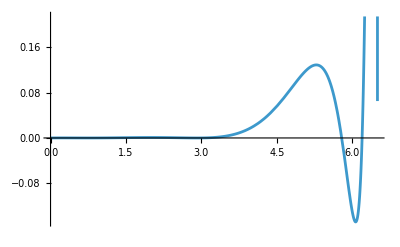

```mathematica
Plot[Det[mat2],{ℰ,0,vpot}]
```

The number of roots of the determinant indicates the number of energy levels of the system, and the value of these roots indicates the amount of energy at each energy level .

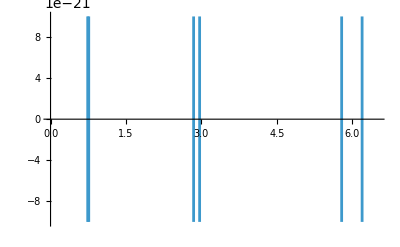

```mathematica
fig=Plot[Det[mat2],{ℰ,0,vpot},PlotRange->{-10^-20,10^-20}]
```

We observe 6 roots, meaning that this system has 6 energy levels.

Finding the eigenvalues of the energy:

```mathematica
approxroots= 
fig[[1,1,1,1,3,1]][[2;;-1]]//Map[#[[1,1,1]]&,#]&//Sort
```

{0.739199,0.7595,2.84476,2.96416,5.78811,6.19469}

```mathematica
rval= approxroots//Map[FindRoot[Det[mat2],{ℰ,#}]&,#]&//
Map[ℰ/.#&,#]&
```

{0.739194,0.759528,2.84474,2.96417,5.78909,6.19471}

### Calculating the energies by levels:

#### Level 1

```mathematica
nval=1;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{0.707107,-0.000103738,-0.000420087,0.0000274377,0.0000274377,-0.000103738,0.000420087,0.707107}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

4.8918×10^-7

Visualizing the wavefunctions and PDFs:

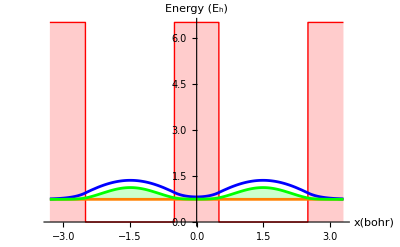

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-0.3,la+lb+0.3} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

No nodes: bonding state.

ORIGIN OF COVALENT BONDING: (tunneling effect) probability of finding the electron in the forbidden region (-lb/2,lb/2).
To know the force of the covalent bonding, we should compute the probability of finding the electron in the forbidden region; if it’s strong, the covalent bond is strong.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (inside the central barrier)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-lb/2,lb/2}]
```

0.0165715

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

1.65735×10^-10

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.44961

Then, Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

1.56512

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.5000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.+6.94417×10^-13 ⅈ and 6.71912×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

1.09625

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

1.04702

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

1.63872

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.548126

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.191068

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

0.739194

```mathematica
ℰ/.ℰ->rval[[nval]]
```

0.739194

#### Level 2

```mathematica
nval=2;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707107,0.000123297,0.000415411,-0.0000265255,0.0000265255,-0.000123297,0.000415411,0.707107}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

4.82117×10^-7

Visualizing the wavefunctions and PDFs:

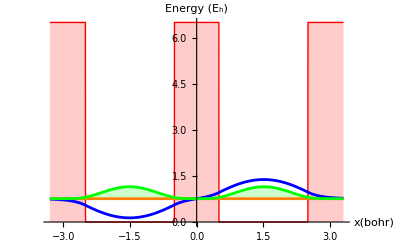

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-0.3,la+lb+0.3} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

Nodes: anti-bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (inside the central barrier)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-lb/2,lb/2}]
```

0.00982309

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.5000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 3.9418×10^-11 and 2.02493×10^-14 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.50693

Then, Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

1.58333

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.5000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 0.-1.69571×10^-13 ⅈ and 2.69846×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

1.21675

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

1.10306

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

1.74651

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.608376

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.151152

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

0.759528

```mathematica
ℰ/.ℰ->rval[[nval]]
```

0.759528

#### Level 3

```mathematica
nval=3;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.707106,0.000486012,0.00114043,-0.00021351,-0.00021351,0.000486012,-0.00114043,0.707106}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

4.30598×10^-6

Visualizing the wavefunctions and PDFs:

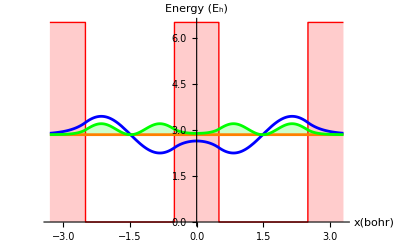

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-0.3,la+lb+0.3} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

No nodes: bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (inside the central barrier)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-lb/2,lb/2}]
```

0.0793953

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.07028}. NIntegrate obtained -6.96203×10^-12 and 1.41097×10^-16 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.73146

Then, Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

1.65271

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.5000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.-2.35281×10^-13 ⅈ and 1.89854×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

3.90633

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

1.97644

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

3.26649

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

1.95317

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.891571

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

2.84474

```mathematica
ℰ/.ℰ->rval[[nval]]
```

2.84474

#### Level 4

```mathematica
nval=4;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707105,-0.000704019,-0.00116066,0.000240478,-0.000240478,0.000704019,-0.00116066,0.707105}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

4.94077×10^-6

Visualizing the wavefunctions and PDFs:

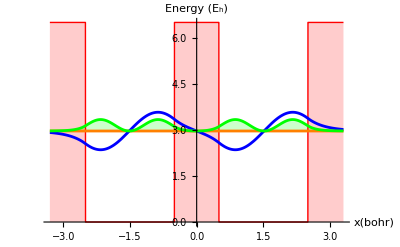

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-0.3,la+lb+0.3} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

Nodes: anti-bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (inside the central barrier)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-lb/2,lb/2}]
```

0.0391605

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.5000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained -7.65869×10^-12 and 2.96632×10^-14 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.87706

Then, Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

1.69619

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.5000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.+3.47861×10^-13 ⅈ and 2.03766×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

4.58778

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.14191

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

3.63309

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.29389

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.670283

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

2.96417

```mathematica
ℰ/.ℰ->rval[[nval]]
```

2.96417

#### Level 5

```mathematica
nval=5;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.705911,-0.0117825,-0.0360802,0.0157672,0.0157672,-0.0117825,0.0360802,0.705911}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.00528687

Visualizing the wavefunctions and PDFs:

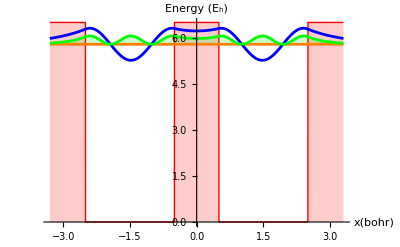

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-0.3,la+lb+0.3} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

No nodes: bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (inside the central barrier)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-lb/2,lb/2}]
```

0.212017

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.4999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 1.12584×10^-14 and 2.82104×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

3.37312

Then, Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

1.83661

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.4999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 0.+5.39499×10^-16 ⅈ and 1.4052×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

6.17611

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.48518

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

4.56429

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

3.08805

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.70104

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

5.78909

```mathematica
ℰ/.ℰ->rval[[nval]]
```

5.78909

#### Level 6

```mathematica
nval=6;
Do[Subscript[c,i]=.,{i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.691614,0.0667736,0.0750336,-0.10762,0.10762,-0.0667736,0.0750336,0.691614}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.0367803

Visualizing the wavefunctions and PDFs:

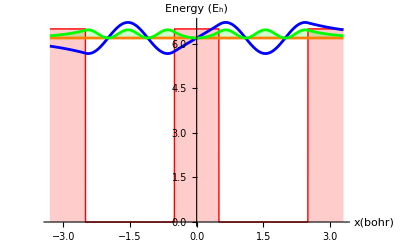

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-0.3,la+lb+0.3} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

Nodes: anti- bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (inside the central barrier)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-lb/2,lb/2}]
```

0.0660754

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.5000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 2.29088×10^-14 and 1.27508×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

4.99442

Then, Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

2.23482

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.5000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.+9.92262×10^-16 ⅈ and 2.10157×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

7.18132

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.6798

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

5.98887

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

3.59066

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.60405

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

6.19471

```mathematica
ℰ/.ℰ->rval[[nval]]
```

6.19471

### Summary of the plots

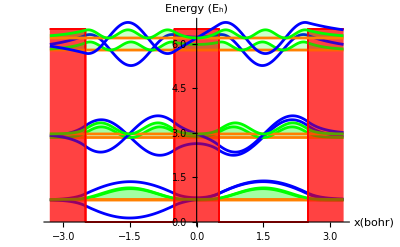

```mathematica
Show@@Table[figure[i],{i,6}]
```

What is the total energy of the system if it has 6 electrons?
1. How many energy levels are occupied?
We put 2 electrons in the 1st level, they can be between the 2 atoms, then other 2 electrons in the 2nd level, and the final 2 in the 3rd energy level. So there are 3 energy levels occupied.

```mathematica
Subscript[ℰ, tot][mol]=2 Sum[rval[[i]],{i,3}]
```

8.68692

2. What is the total kinetic energy of the 6 electrons?

```mathematica
Subscript[k, tot]=2 Sum[⟨Subscript[k, i]⟩,{i,3}]
```

6.21933

3. What is the total potential energy of 6 electrons?

```mathematica
Subscript[u, tot]=2 Sum[⟨Subscript[u, i]⟩,{i,3}]
```

2.46758

Notice that ℰ_tot = k_tot + u_tot:

```mathematica
Subscript[k, tot]+Subscript[u, tot]
```

8.68692

### Cohesion energy

ℰ_coh = ℰ[mol]/N - ℰ[atom]

N represents the number of atoms.
ℰ[atom] is the energy of one atom

The atom/molecule tends to go to a lower energy to be more stable, so the energy that is lower, indicates what happen with the atom/molecule.
More negative the value, more stronger is the bond.

What is the cohesion energy when the molecule has 6 electrons?

1. First, let’s recall ℰ[atom] values for the single atom. 
(that can be found in rval (values of the energy levels) ).

```mathematica
rvalsingle={0.7495002092226133,2.903204974570781,5.927144023424667}
```

{0.7495,2.9032,5.92714}

2. Now, let’s calculate the energy for the single atom.
(Note that there are 6 electrons in the whole system (molecule) but 3 electron in the single atom).

```mathematica
ℰatom=2(rvalsingle[[1]])+rvalsingle[[2]]
```

4.40221

3. Now, we can proceed to recover the energies for the diatomic molecule.

```mathematica
dirval={0.7391935544790608,0.7595280391915434,2.8447366422983,2.9641749400272097,5.789094229753914,6.194709437833919}
```

{0.739194,0.759528,2.84474,2.96417,5.78909,6.19471}

4. Following, we can calculate the ℰ[mol] .
(The diatomic molecule has 6 electrons).

```mathematica
ℰdimol=2(dirval[[1]]+dirval[[2]]+dirval[[3]])
```

8.68692

5. Computing the ℰ cohesion for the diatomic molecule:

```mathematica
Subscript[ℰ, dicoh]=ℰdimol/2-ℰatom
```

-0.0587472

What is the cohesion energy when the system has 8 electrons?

1. First, let’s recall ℰ[atom] values for the single atom.

```mathematica
rvalsingle={0.7495002092226133,2.903204974570781,5.927144023424667}
```

{0.7495,2.9032,5.92714}

2. Now, let’s calculate the energy for the single atom.
(each atom contributes with 4 electron to the system, so the #’s of ℯ is 4).

```mathematica
ℰatom=2(rvalsingle[[1]]+rvalsingle[[2]])
```

7.30541

3. Now, we can proceed to recover the energies for the diatomic molecule.

```mathematica
dirval={0.7391935544790608,0.7595280391915434,2.8447366422983,2.9641749400272097,5.789094229753914,6.194709437833919}
```

{0.739194,0.759528,2.84474,2.96417,5.78909,6.19471}

4. Now we can calculate the ℰ[mol] when the molecule has 8 ℯ:

```mathematica
ℰdimol=2(dirval[[1]]+dirval[[2]]+dirval[[3]]+dirval[[4]])
```

14.6153

5. Proceed to calculate the ℰ cohesion for the diatomic molecule:

```mathematica
Subscript[ℰ, dicoh]=ℰdimol/2-ℰatom
```

-10.9626

What is the cohesion energy when the system has 10 electrons, each atom contributes with 5 ℯ?

1. First, let’s recall ℰ[atom] values for the single atom.

```mathematica
rvalsingle={0.7495002092226133,2.903204974570781,5.927144023424667}
```

{0.7495,2.9032,5.92714}

2. Now, let’s calculate the energy for the single atom.
(each atom contributes with 5 electron to the system, so the #’s of ℯ is 5).

```mathematica
ℰatom=2(rvalsingle[[1]]+rvalsingle[[2]])+rvalsingle[[3]]
```

7.30541

3. Now, we can proceed to recover the energies for the diatomic molecule.

```mathematica
dirval={0.7391935544790608,0.7595280391915434,2.8447366422983,2.9641749400272097,5.789094229753914,6.194709437833919}
```

{0.739194,0.759528,2.84474,2.96417,5.78909,6.19471}

4. Now we can calculate the ℰ[mol] when the molecule has 10 ℯ:

```mathematica
ℰdimol=2(dirval[[1]]+dirval[[2]]+dirval[[3]]+dirval[[4]]+dirval[[5]])
```

14.6153

5. Proceed to calculate the ℰ cohesion for the diatomic molecule:

```mathematica
Subscript[ℰ, dicoh]=ℰdimol/2-ℰatom
```

-10.9626

## Three Finite Potential Wells: Model of a Triatomic Molecule

### Define the potential:

Let’s define the potential and visualize (for inserting {, use EscpwEsc, and to add spaces, use Ctrlenter):

```mathematica
v[x_]:= Piecewise[{{v0, x<-3/2 a-b}, {0, -3/2 a-b<= x <=-a/2-b}, {v0, -a/2-b<x<-a/2}, {0, -a/2<=x<=a/2}, {v0, a/2<x<b+a/2}, {0, b+a/2<=x<= 3/2 a+b}, {v0, x>3/2 a+b}}]
```

Setting values of the variables : width (a) and height (v0pot) of the potential :

```mathematica
la=2 (*Bohr*);
lb=1 (*Bohr*);
vpot = 6.5 (*Subscript[E, h] (Hartree)*);
```

Visualizing the potential:

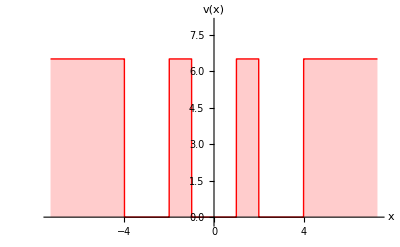

```mathematica
Plot[ v[x]/.{v0-> vpot,a->la,b->lb}, {x,-3la-lb-0.3,3la+lb+0.3} ,
AxesLabel->{"x","v(x)"},
PlotStyle->{Red, Thick},
PlotRange->{Automatic,{-0.2,vpot+1.5}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis
]
```

### Solving the Schrodinger equation in a.u

In atomic units: ℏ → 1, m→ 1, e → 1. Then, lengths are given in Bohr (1 Bohr = 0.53 Å) and energies in Hartree (E_h =2721 eV).

Let's define α =√(2 (v0 - ℰ)), β =√(2 ℰ), where ℰ is the energy (ℰ is EscscEEsc and ϕ is EscfEsc):

We have 7 regions (7 associated wavefunctions), and 6 BCs.
In regions where V = 0, the solution take the form of cos(x) + sin(x). On the other hand, in regions where V = v0, the solutions take the form of exponentials.

```mathematica
Do[Subscript[c,i]= .,{i,12}];
Do[Subscript[ϕ, i]=.,{i,7}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
Subscript[ϕ, 2][x_]:=Subscript[c, 2] Cos[β x]+ Subscript[c, 3] Sin [β x];
Subscript[ϕ, 3][x_]:=Subscript[c, 4] Exp[-α x]+Subscript[c, 5] Exp[α x];
Subscript[ϕ, 4][x_]:=Subscript[c, 6] Cos[β x]+Subscript[c, 7] Sin[β x];
Subscript[ϕ, 5][x_]:=Subscript[c, 8] Exp[-α x]+Subscript[c, 9] Exp[α x];
Subscript[ϕ, 6][x_]:=Subscript[c, 10] Cos[β x]+Subscript[c, 11] Sin[β x];
Subscript[ϕ, 7][x_]:=Subscript[c, 12] Exp[-α x];
```

Unset::norep: Assignment on Subscript for c_9 not found.

Unset::norep: Assignment on Subscript for c_10 not found.

Unset::norep: Assignment on Subscript for c_11 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ϕ_1 not found.

Unset::norep: Assignment on Subscript for ϕ_2 not found.

Unset::norep: Assignment on Subscript for ϕ_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Let’s define the wavefunction ϕ (x):

(φ is EscjEsc)

```mathematica
ϕ[x_]:=Piecewise[{{Subscript[ϕ, 1][x], x<-3/2 a-b}, {Subscript[ϕ, 2][x], -3/2 a-b<= x <=-a/2-b}, {Subscript[ϕ, 3][x], -a/2-b<x<-a/2}, {Subscript[ϕ, 4][x], -a/2<=x<=a/2}, {Subscript[ϕ, 5][x], a/2<x<b+a/2}, {Subscript[ϕ, 6][x], b+a/2<=x<= 3/2 a+b}, {Subscript[ϕ, 7][x], x>3/2 a+b}}]
```

Defining the BCs:

```mathematica
eq[1]=(Subscript[ϕ, 1][x]-Subscript[ϕ, 2][x]/. x->-3/2 a-b)==0;
eq[2]=(Subscript[ϕ, 1]'[x]-Subscript[ϕ, 2]'[x]/. x->-3/2 a-b)==0;
eq[3]=(Subscript[ϕ, 2][x]-Subscript[ϕ, 3][x]/. x->-a/2-b )==0;
eq[4]=(Subscript[ϕ, 2]'[x]-Subscript[ϕ, 3]'[x]/. x->-a/2-b )==0;
eq[5]=(Subscript[ϕ, 3][x]-Subscript[ϕ, 4][x]/. x->-a/2 )==0;
eq[6]=(Subscript[ϕ, 3]'[x]-Subscript[ϕ, 4]'[x]/. x->-a/2 )==0;
eq[7]=(Subscript[ϕ, 4][x]-Subscript[ϕ, 5][x]/. x->a/2 )==0;
eq[8]=(Subscript[ϕ, 4]'[x]-Subscript[ϕ, 5]'[x]/. x->a/2 )==0;
eq[9]=(Subscript[ϕ, 5][x]-Subscript[ϕ, 6][x]/. x->b+a/2 )==0;
eq[10]=(Subscript[ϕ, 5]'[x]-Subscript[ϕ, 6]'[x]/. x->b+a/2 )==0;
eq[11]=(Subscript[ϕ, 6][x]-Subscript[ϕ, 7][x]/. x->3/2 a+b )==0;
eq[12]=(Subscript[ϕ, 6]'[x]-Subscript[ϕ, 7]'[x]/. x->3/2 a+b )==0;
```

Solving the BC equations

The way to solve this is by making the determinant of the matrix of the BCs equations == 0.

```mathematica
mat = CoefficientArrays[Table[eq[i],{i,12}], Table[Subscript[c, i],{i,12}]][[2]]//Normal
```

{{ⅇ^((-(3 a)/2-b) α),-Cos[(-(3 a)/2-b) β],-Sin[(-(3 a)/2-b) β],0,0,0,0,0,0,0,0,0},{ⅇ^((-(3 a)/2-b) α) α,β Sin[(-(3 a)/2-b) β],-β Cos[(-(3 a)/2-b) β],0,0,0,0,0,0,0,0,0},{0,Cos[(-a/2-b) β],Sin[(-a/2-b) β],-ⅇ^(-((-a/2-b) α)),-ⅇ^((-a/2-b) α),0,0,0,0,0,0,0},{0,-β Sin[(-a/2-b) β],β Cos[(-a/2-b) β],ⅇ^(-((-a/2-b) α)) α,-ⅇ^((-a/2-b) α) α,0,0,0,0,0,0,0},{0,0,0,ⅇ^((a α)/2),ⅇ^(-(a α)/2),-Cos[(a β)/2],Sin[(a β)/2],0,0,0,0,0},{0,0,0,-ⅇ^((a α)/2) α,ⅇ^(-(a α)/2) α,-β Sin[(a β)/2],-β Cos[(a β)/2],0,0,0,0,0},{0,0,0,0,0,Cos[(a β)/2],Sin[(a β)/2],-ⅇ^(-(a α)/2),-ⅇ^((a α)/2),0,0,0},{0,0,0,0,0,-β Sin[(a β)/2],β Cos[(a β)/2],ⅇ^(-(a α)/2) α,-ⅇ^((a α)/2) α,0,0,0},{0,0,0,0,0,0,0,ⅇ^(-((a/2+b) α)),ⅇ^((a/2+b) α),-Cos[(a/2+b) β],-Sin[(a/2+b) β],0},{0,0,0,0,0,0,0,-ⅇ^(-((a/2+b) α)) α,ⅇ^((a/2+b) α) α,β Sin[(a/2+b) β],-β Cos[(a/2+b) β],0},{0,0,0,0,0,0,0,0,0,Cos[((3 a)/2+b) β],Sin[((3 a)/2+b) β],-ⅇ^(-(((3 a)/2+b) α))},{0,0,0,0,0,0,0,0,0,-β Sin[((3 a)/2+b) β],β Cos[((3 a)/2+b) β],ⅇ^(-(((3 a)/2+b) α)) α}}

```mathematica
mat//MatrixForm
```

(ⅇ^((-(3 a)/2-b) α) | -Cos[(-(3 a)/2-b) β] | -Sin[(-(3 a)/2-b) β] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅇ^((-(3 a)/2-b) α) α | β Sin[(-(3 a)/2-b) β] | -β Cos[(-(3 a)/2-b) β] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Cos[(-a/2-b) β] | Sin[(-a/2-b) β] | -ⅇ^(-((-a/2-b) α)) | -ⅇ^((-a/2-b) α) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -β Sin[(-a/2-b) β] | β Cos[(-a/2-b) β] | ⅇ^(-((-a/2-b) α)) α | -ⅇ^((-a/2-b) α) α | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^((a α)/2) | ⅇ^(-(a α)/2) | -Cos[(a β)/2] | Sin[(a β)/2] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅇ^((a α)/2) α | ⅇ^(-(a α)/2) α | -β Sin[(a β)/2] | -β Cos[(a β)/2] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Cos[(a β)/2] | Sin[(a β)/2] | -ⅇ^(-(a α)/2) | -ⅇ^((a α)/2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -β Sin[(a β)/2] | β Cos[(a β)/2] | ⅇ^(-(a α)/2) α | -ⅇ^((a α)/2) α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-((a/2+b) α)) | ⅇ^((a/2+b) α) | -Cos[(a/2+b) β] | -Sin[(a/2+b) β] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(-((a/2+b) α)) α | ⅇ^((a/2+b) α) α | β Sin[(a/2+b) β] | -β Cos[(a/2+b) β] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[((3 a)/2+b) β] | Sin[((3 a)/2+b) β] | -ⅇ^(-(((3 a)/2+b) α))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -β Sin[((3 a)/2+b) β] | β Cos[((3 a)/2+b) β] | ⅇ^(-(((3 a)/2+b) α)) α)

```mathematica
mat2=mat/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb}//FullSimplify
```

{{ⅇ^(-5.65685 √(6.5-ℰ)),-Cos[4 √2 √ℰ],Sin[4 √2 √ℰ],0,0,0,0,0,0,0,0,0},{1.41421 ⅇ^(-5.65685 √(6.5-ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[4 √2 √ℰ],-√2 √ℰ Cos[4 √2 √ℰ],0,0,0,0,0,0,0,0,0},{0,Cos[2 √2 √ℰ],-Sin[2 √2 √ℰ],-ⅇ^(2.82843 √(6.5-ℰ)),-ⅇ^(-2.82843 √(6.5-ℰ)),0,0,0,0,0,0,0},{0,√2 √ℰ Sin[2 √2 √ℰ],√2 √ℰ Cos[2 √2 √ℰ],1.41421 ⅇ^(2.82843 √(6.5-ℰ)) √(6.5-ℰ),-1.41421 ⅇ^(-2.82843 √(6.5-ℰ)) √(6.5-ℰ),0,0,0,0,0,0,0},{0,0,0,ⅇ^(1.41421 √(6.5-ℰ)),ⅇ^(-1.41421 √(6.5-ℰ)),-Cos[√2 √ℰ],Sin[√2 √ℰ],0,0,0,0,0},{0,0,0,-1.41421 ⅇ^(1.41421 √(6.5-ℰ)) √(6.5-ℰ),1.41421 ⅇ^(-1.41421 √(6.5-ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[√2 √ℰ],-√2 √ℰ Cos[√2 √ℰ],0,0,0,0,0},{0,0,0,0,0,Cos[√2 √ℰ],Sin[√2 √ℰ],-ⅇ^(-1.41421 √(6.5-ℰ)),-ⅇ^(1.41421 √(6.5-ℰ)),0,0,0},{0,0,0,0,0,-√2 √ℰ Sin[√2 √ℰ],√2 √ℰ Cos[√2 √ℰ],1.41421 ⅇ^(-1.41421 √(6.5-ℰ)) √(6.5-ℰ),-1.41421 ⅇ^(1.41421 √(6.5-ℰ)) √(6.5-ℰ),0,0,0},{0,0,0,0,0,0,0,ⅇ^(-2.82843 √(6.5-ℰ)),ⅇ^(2.82843 √(6.5-ℰ)),-Cos[2 √2 √ℰ],-Sin[2 √2 √ℰ],0},{0,0,0,0,0,0,0,-1.41421 ⅇ^(-2.82843 √(6.5-ℰ)) √(6.5-ℰ),1.41421 ⅇ^(2.82843 √(6.5-ℰ)) √(6.5-ℰ),√2 √ℰ Sin[2 √2 √ℰ],-√2 √ℰ Cos[2 √2 √ℰ],0},{0,0,0,0,0,0,0,0,0,Cos[4 √2 √ℰ],Sin[4 √2 √ℰ],-ⅇ^(-5.65685 √(6.5-ℰ))},{0,0,0,0,0,0,0,0,0,-√2 √ℰ Sin[4 √2 √ℰ],√2 √ℰ Cos[4 √2 √ℰ],1.41421 ⅇ^(-5.65685 √(6.5-ℰ)) √(6.5-ℰ)}}

Plotting the determinant:

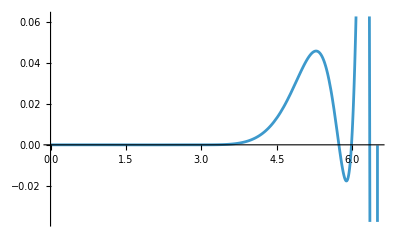

```mathematica
Plot[Det[mat2],{ℰ,0, vpot}]
```

The number of roots of the determinant indicates the number of energy levels of the system, and the value of these roots indicates the amount of energy at each energy level .

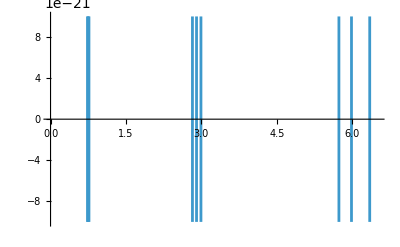

```mathematica
fig=Plot[Det[mat2],{ℰ,0,vpot},PlotRange->{-10^-20,10^-20}]
```

We observe 9 roots, meaning that this system has 9 energy levels.

Finding the eigenvalues of the energy:

```mathematica
approxroots= 
fig[[1,1,1,1,3,1]][[2;;-1]]//Map[#[[1,1,1]]&,#]&//Sort
```

{0.735003,0.749238,0.763652,2.82144,2.90276,2.99045,5.73363,5.98363,6.34613}

```mathematica
rval= approxroots//Map[FindRoot[Det[mat2],{ℰ,#}]&,#]&//
Map[ℰ/.#&,#]&
```

{0.734976,0.749237,0.76373,2.82139,2.90277,2.99047,5.73363,5.98363,6.34616}

### Calculating the energies by levels

#### Level 1

```mathematica
nval=1;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{0.707107,-2.35466×10^-6,1.22652×10^-6,1.04049×10^-9,0.0000387152,3.78837×10^-6,0,0.0000387152,1.04049×10^-9,-2.35466×10^-6,-1.22653×10^-6,0.707107}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

3.72987×10^-11

Visualizing the wavefunctions and PDFs:

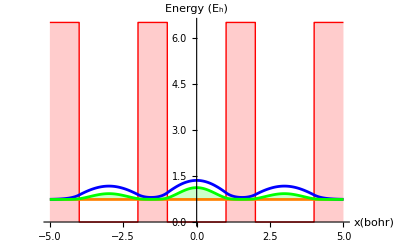

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-2, la+lb+2} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

No nodes: bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (between the central barriers)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,la/2,lb+la/2}]
```

0.0121829

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

4.64783

Therefore then Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

2.15588

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

1.07139

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

1.03508

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

2.23151

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.535694

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.199283

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

0.734976

```mathematica
ℰ/.ℰ->rval[[nval]]
```

0.734976

#### Level 2

```mathematica
nval=2;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707107,2.3066×10^-6,-1.35301×10^-6,-1.02945×10^-9,-6.98865×10^-7,0,5.75311×10^-8,6.98942×10^-7,1.02945×10^-9,-2.3066×10^-6,-1.35301×10^-6,0.707107}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.85273×10^-11

Visualizing the wavefunctions and PDFs:

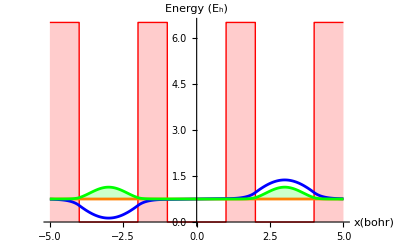

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-2, la+lb+2} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

No nodes: bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (between the central barriers)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,la/2,lb+la/2}]
```

0.0066427

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

9.22532

Therefore then Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

3.03732

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

1.15522

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

1.07481

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

3.26455

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.577611

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.171626

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

0.749237

```mathematica
ℰ/.ℰ->rval[[nval]]
```

0.749237

#### Level 3

```mathematica
nval=3;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.707107,-2.25209×10^-6,1.47904×10^-6,1.01746×10^-9,-0.0000375897,-3.77483×10^-6,0,-0.0000375897,1.01746×10^-9,-2.25209×10^-6,-1.47904×10^-6,0.707107}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

3.68009×10^-11

Visualizing the wavefunctions and PDFs:

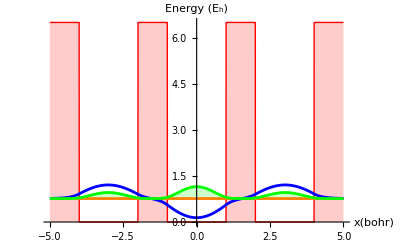

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-2, la+lb+2} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

Nodes: anti-bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (between the central barriers)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,la/2,lb+la/2}]
```

0.0075673

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

4.81129

Therefore then Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

2.19346

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

1.24175

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

1.11434

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

2.44426

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.620876

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.142854

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

0.76373

```mathematica
ℰ/.ℰ->rval[[nval]]
```

0.76373

#### Level 4

```mathematica
nval=4;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707107,0.0000148909,0.0000145698,6.09589×10^-8,0.000294205,0,-0.0000294891,-0.000294205,-6.09589×10^-8,-0.0000148909,0.0000145698,0.707107}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

2.45375×10^-9

Visualizing the wavefunctions and PDFs:

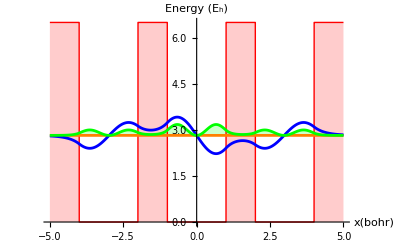

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-2, la+lb+2} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

No nodes: bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (between the central barriers)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,la/2,lb+la/2}]
```

0.0574589

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

4.9508

Therefore then Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

2.22504

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

3.78088

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

1.94445

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

4.32647

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

1.89044

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.93095

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

2.82139

```mathematica
ℰ/.ℰ->rval[[nval]]
```

2.82139

#### Level 5

```mathematica
nval=5;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.707107,-0.0000187817,-0.0000135742,-7.24756×10^-8,-1.6508×10^-6,1.57629×10^-6,0,-1.6508×10^-6,-7.24756×10^-8,-0.0000187817,0.0000135742,0.707107}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

1.4765×10^-9

Visualizing the wavefunctions and PDFs:

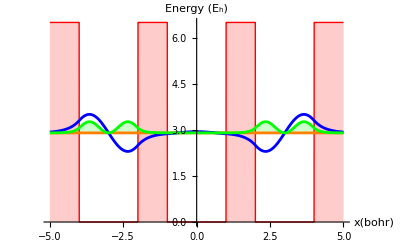

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-2, la+lb+2} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

No nodes: bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (between the central barriers)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,la/2,lb+la/2}]
```

0.0303027

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

9.53588

Therefore then Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

3.08802

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.0000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.-2.95397×10^-10 ⅈ and 1.97413×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

4.23045

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.05681

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

6.35147

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.11523

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.787543

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

2.90277

```mathematica
ℰ/.ℰ->rval[[nval]]
```

2.90277

#### Level 6

```mathematica
nval=6;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707107,0.0000232449,0.0000117421,8.71578×10^-8,-0.000349959,0,0.0000366659,0.000349959,-8.71578×10^-8,-0.0000232449,0.0000117421,0.707107}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

3.58269×10^-9

Visualizing the wavefunctions and PDFs:

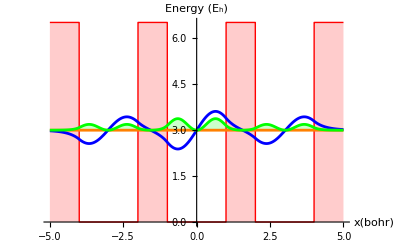

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-2, la+lb+2} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

Nodes: anti-bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (between the central barriers)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,la/2,lb+la/2}]
```

0.030995

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

5.18218

Therefore then Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

2.27644

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-3.9999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 0.-5.42498×10^-11 ⅈ and 1.04712×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

4.74773

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.17893

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

4.9602

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.37386

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

0.616609

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

2.99047

```mathematica
ℰ/.ℰ->rval[[nval]]
```

2.99047

#### Level 7

```mathematica
nval=7;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.706805,0.00430286,-0.00312713,0.000306164,0.0193428,-0.00686909,0,0.0193428,0.000306164,0.00430286,0.00312713,0.706805}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.000187818

Visualizing the wavefunctions and PDFs:

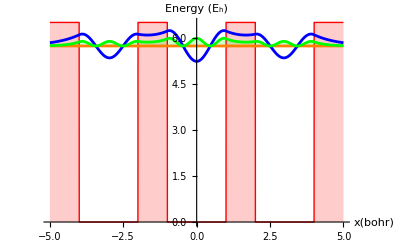

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-2, la+lb+2} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

No nodes: bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (between the central barriers)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,la/2,lb+la/2}]
```

0.151133

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-3.9999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 2.05547×10^-13 and 2.46452×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

5.94924

Therefore then Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

2.43911

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.0000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.-1.85728×10^-14 ⅈ and 4.33728×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

6.14248

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.4784

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

6.04509

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

3.07124

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.66239

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

5.73363

```mathematica
ℰ/.ℰ->rval[[nval]]
```

5.73363

#### Level 8

```mathematica
nval=8;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.706904,-0.00698728,0.0105403,-0.0017447,0.0109703,0,-0.00271858,-0.0109703,0.0017447,0.00698728,0.0105403,0.706904}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.000587414

Visualizing the wavefunctions and PDFs:

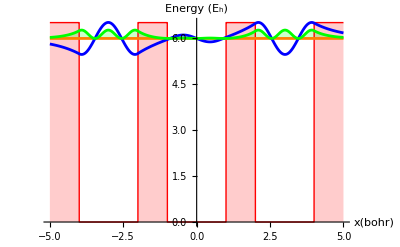

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-2, la+lb+2} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

No nodes: bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (between the central barriers)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,la/2,lb+la/2}]
```

0.0753924

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-3.9999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained -1.45026×10^-13 and 4.66138×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

11.048

Therefore then Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

3.32386

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.0000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.-2.96464×10^-15 ⅈ and 1.48055×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

6.80117

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.60791

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

8.66831

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

3.40059

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.58307

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

5.98366

```mathematica
ℰ/.ℰ->rval[[nval]]
```

5.98363

#### Level 9

```mathematica
nval=9;
Do[Subscript[c,i]=.,{i,12}];
Evaluate[Table[Subscript[c, i],{i,12}]]=
(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.610895,0.00276313,-0.067175,0.0537556,-0.33678,0.109335,0,-0.33678,0.0537556,0.00276313,0.067175,0.610895}

We need to find the normalization constant for φ(x) (∞ is EscinfEsc):

```mathematica
int=NIntegrate[Abs[ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//Evaluate,{x,-∞,∞}]
```

0.0359037

Visualizing the wavefunctions and PDFs:

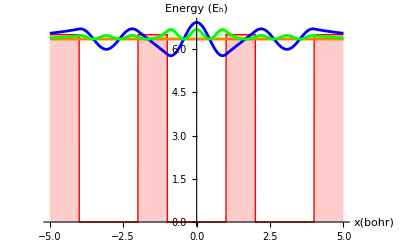

```mathematica
figure[nval]=Plot[
{
v[x],
ℰ,
ℰ+1/(√int)ϕ[x],
ℰ+(1/(√int)ϕ[x])^2,
}/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}//
Evaluate, {x,-la-lb-2, la+lb+2} ,
PlotRange->All,
AxesLabel->{"x(bohr)","Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->12},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

Nodes: anti-bonding state.

Overall probability of the wave function must be 1:

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]
```

1.

What is the probability of finding one electron at - lb/2 < x < +lb/2 (between the central barriers)?

```mathematica
NIntegrate[Abs[1/(√int)ϕ[x]]^2/.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,la/2,lb+la/2}]
```

0.06805

Heisenberg Uncertainty Principle

Δp Δx ≥ ℏ/2

Δx is the standard deviation (uncertainty) of position, Δx = √(⟨x^2⟩-⟨x⟩^2),
Δp is the standard deviation (uncertainty) of momentum, Δp = √(⟨p^2⟩-⟨p⟩^2)

1. Let’s find the uncertainty of position Δx:
We need the expected value of ⟨x^2⟩ and ⟨x⟩.
The expected value is: ,,⟨ ô ⟩ = ∫(ψ*)ô (ψ)ⅆx

```mathematica
⟨x⟩=NIntegrate[1/(√int)ϕ[x]* x 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-3.9999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 4.80865×10^-15 and 2.28296×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[1/(√int)ϕ[x]* x^2 1/(√int)ϕ[x] /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

8.40386

Therefore then Δx is:

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

2.89894

2. Let’s find the uncertainty of momentum Δp:
We need the expected value of ⟨p^2⟩ and ⟨p⟩.

```mathematica
⟨p⟩=NIntegrate[1/(√int)ϕ[x]* (-ⅈ D[  1/(√int)ϕ[x],x]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop[#,10^-5]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.0000000358703643196300000453675071131198759388780672452412545681}. NIntegrate obtained 0.-1.47105×10^-15 ⅈ and 1.13903×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)ϕ[x]* (-D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

8.04229

Then, Δp is:

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.83589

Therefore, Heisenberg uncertainty principle Δx Δp gives:

```mathematica
Δx Δp
```

8.22109

The result must be bigger or equal to ℏ/2 but since in a.u ℏ ->1, then the result must be bigger or equal to 1/2, which is the case.

What is the expected value of the kinetic energy for this level?

```mathematica
⟨Subscript[k, nval]⟩ = NIntegrate[1/(√int)ϕ[x]* (-1/2 D[  1/(√int)ϕ[x],{x,2}]) /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

4.02115

What is the expected value of the potential energy of this level?

```mathematica
⟨Subscript[u, nval]⟩=NIntegrate[1/(√int)ϕ[x]* v[x] 1/(√int) ϕ[x]  /.{α->√(2 (v0 - ℰ)), β-> √(2 ℰ)}/.{v0->vpot,a->la,b->lb,ℰ->rval[[nval]]}// Evaluate,{x,-∞,∞}]//Chop
```

2.32501

What is the total energy of the level?

```mathematica
etotal=⟨Subscript[k, nval]⟩ +⟨Subscript[u, nval]⟩
```

6.34616

```mathematica
ℰ/.ℰ->rval[[nval]]
```

6.34616

### Summary of the plots

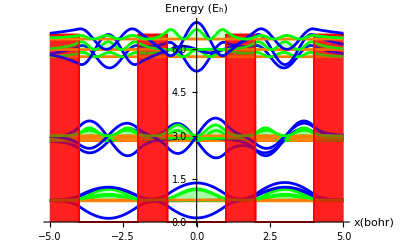

```mathematica
Show@@Table[figure[i],{i,9}]
```

What is the total energy of the system if it has 6 electrons?
1. How many energy levels are occupied?

```mathematica
Subscript[ℰ, tot][mol]=3 Sum[rval[[i]],{i,2}]
```

4.45264

2. What is the total kinetic energy of the 6 electrons?

```mathematica
Subscript[k, tot] 3 Sum[⟨Subscript[k, i]⟩,{i,1,2}]
```

20.7721

3. What is the total potential energy of 3 electrons?

```mathematica
Subscript[u, tot]=3Sum[⟨Subscript[u, i]⟩,{i,2}]
```

1.11272

Notice that ℰ_tot = k_tot + u_tot:

```mathematica
Subscript[k, tot]+Subscript[u, tot]
```

7.33206

### Cohesion energy

ℰ_coh:   ℰ[mol]/N - ℰ[atom]

N represents the number of atoms.
ℰ[atom] is the energy of one atom

The atom/molecule tends to go to a lower energy to be more stable, so the energy that is lower, indicates what happen with the atom/molecule.
More negative the value, more stronger is the bond.

What is the cohesion energy when the molecule has 6 electrons?

1. First, let’s recall ℰ[atom] values for the single atom. 
(that can be found in rval (values of the energy levels) )

```mathematica
rvalsingle={0.7495002092226133,2.903204974570781,5.927144023424667}
```

{0.7495,2.9032,5.92714}

2. Now, let’s calculate the energy for the single atom.
(Note that there are 6 electrons in the whole system (molecule) but 3 electrons in the single atom)

```mathematica
ℰatom=2(rvalsingle[[1]])
```

1.499

3. Now, we can proceed to recover the energies for the triatomic molecule.

```mathematica
trirval={0.7349763766287658,0.7492368476290246,0.7637297046436409,2.8213876929154207,2.902769684405238,2.990473047146399,5.733626866559861,5.983631301161692,6.34616022481897};
```

4. Following, we can calculate the ℰ[mol] .
(The triatomic molecule has 6 electrons)

```mathematica
ℰtrimol=2(trirval[[1]]+trirval[[2]]+trirval[[3]])
```

4.49589

5. Computing the ℰ cohesion for the triatomic molecule:

```mathematica
Subscript[ℰ, dicoh]=ℰtrimol/2-ℰatom
```

0.748943

What is the cohesion energy when the molecule has 9 electrons?

1. First, let’s recall ℰ[atom] values for the single atom.

```mathematica
rvalsingle={0.7495002092226133,2.903204974570781,5.927144023424667}
```

{0.7495,2.9032,5.92714}

2. Now, let’s calculate the energy for the single atom.
(each atom contributes with 3 electron to the system, so the #’s of ℯ is 3)

```mathematica
ℰatom=2(rvalsingle[[1]])+rvalsingle[[2]]
```

4.40221

3. Now, we can proceed to recover the energies for the triatomic molecule.

```mathematica
trirval={0.7349763766287658,0.7492368476290246,0.7637297046436409,2.8213876929154207,2.902769684405238,2.990473047146399,5.733626866559861,5.983631301161692,6.34616022481897};
```

4. Now we can calculate the ℰ[mol] when the molecule has 9 ℯ:

```mathematica
ℰtrimol=2(trirval[[1]]+trirval[[2]]+trirval[[3]]+trirval[[4]])+trirval[[5]]
```

13.0414

5. Proceed to calculate the ℰ cohesion for the triatomic molecule:

```mathematica
Subscript[ℰ, tricoh]=ℰtrimol/2-ℰatom
```

2.11851